## Foreword, etc.

## Pre-amble

```mathematica
AppendTo[$Path,"C:\\Users\\deroo\\__DATA\\MEGA\\DATA\\git\\MFDSNT\\Mathematica Notebooks"];
<<BKPNumberTheory`
```

### Test

```mathematica
nCollatz[5]
```

{5,16,8,4,2,1}

### Transfer to PKG

```mathematica
nDP[f_, g_] := Function[a, DivisorSum[a, f[#] g[a/#] &]]
```

```mathematica
nPrimesLEqThan[n_]:=Prime[Range[PrimePi[n]]]
nPrimesBetween[n_,m_]:=Module[
{a1,a2,rng},
If[n<=m,a1=m;a2=n,a1=n;a2=m];
rng=Complement[nPrimesLEqThan[a1],nPrimesLEqThan[a2]];
rng]
nPrimesBetween[100,150]
```

{101,103,107,109,113,127,131,137,139,149}

## Topic

### Definition / Theorem

This is text.

#### Example

## *Table of Arithmetical Functions ( -under construction- )

### Definition

#### Table

```mathematica
TableForm[{
{"Cell["I",ExpressionUUID->"77878252-9a1d-4b58-b066-202a47535308"]","-","Floor[1/n]","-","CM","I","?","1","1"},
{"1","-","1","-","CM","μ","?",DirichletTransform[1,n,s]//TraditionalForm,"1/(1-x)"},
{"N","-","n","-","CM","μN","?",DirichletTransform[n,n,s]//TraditionalForm,"1/(1-px)"},
{"N^a","a⩾0","n^a","σ_a*μ ; J_a*1","CM","μN^a","x^(a + 1)/(a+1)+O(x^a)",DirichletTransform[n^a,n,s]//TraditionalForm,"1/(1-p^ax)"},
{"μ","Sum of primitive\nn-th roots of unity","MoebiusMu[n]","-","M","1","?",DirichletTransform[MoebiusMu[n],n,s]//TraditionalForm,"1-x"},
{"μ_k","Möbius function of order k","nMoebiusMu[k,n]","-","M","?","?","?","?"},
{"ϕ","Euler Totient function","EulerPhi[n]","μ*N","M","μN*1","3/π^2 x^2 + O(x Log[x])",DirichletTransform[EulerPhi[n],n,s]//TraditionalForm,"(1-x)/(1-px)"},
{"J_k","Jordan Totient function","nJordanTotient[k,n]","μ*N^k ; σ_k*μ*μ","M","μN^k*1","?",DirichletTransform[DirichletConvolve[j^k,MoebiusMu[j],j,n],n,s]//TraditionalForm,"(p^k-1)/(1-p^kx)"},
{"τ","-","DivisorSigma[0,n]","1*1","M","μ*μ","x Log[x]+(2γ-1)x+O(√x)",DirichletTransform[DivisorSigma[0,n],n,s]//TraditionalForm,"1/(1-x)^2"},
{"τ^(k)","The number of ways of expressing n\nas a product of k positive factors","nDirichletPower\n[DivisorSigma[0,#]&,k][n]","1^(k + 1)","M","μ^(k + 1)","?","?","?"},
{"σ","-","DivisorSigma[1,n]","N*1 ; σ=ϕ*τ","M","μ*μN","ζ(2)/2 x^2+O(x Log[x])",DirichletTransform[DivisorSigma[1,n],n,s]//TraditionalForm,"1/((1-px)(1-x))"},
{"σ_a","a≥2","DivisorSigma[a,n]","N^a*1 ; σ_1=ϕ*τ","M","μ*μN^a","ζ(a+1)/(a+1)x^(a + 1)+O(x^a)","s-a s","1/((1-p^ax)(1-x))"},
{"GCD_k","-","GCD[k,n]","-","M","μGCD_k","?","?","?"},
{"γ","Core","-","-","M","?","?","?","(1-(1-p)x)/(1-x)"},
{"λ","-","LiouvilleLambda[n]\n(-1)^PrimeOmega[n]","-","M","μ^2 ; |μ|","?",DirichletTransform[LiouvilleLambda[n],n,s]//TraditionalForm,"1/(1+x)"},
{"μ^2","1 if squarefree, 0 otherwise","-","-","M","λ","?","ζ(s)/ζ(2s)","1+x"},
{"λ*1","1 if square, 0 otherwise","-","-","M","μ^2*μ","?","?","?"},
{"μ^2*1","Number of square-free divisors","2^PrimeNu[n]","|μ|*1","M","λ*μ","?",DirichletTransform[DirichletConvolve[1,Abs[MoebiusMu[j]],j,n],n,s]//TraditionalForm,"(1+x)/(1-x)"},
{"a","Number of abelian groups","FiniteAbelianGroupCount[n]","-","M","?","?","?","?"},
{"ϕ_k","Euler Totient function of order k","nEulerPhi[k,n]","Faulhaber_k*μN^k","-","?","?","?","?"},
{"ν","-","PrimeNu[n]","-","A","None","?","?","?"},
{"Ω","-","PrimeOmega[n]","-","CA","None","?","?","?"},
{"Λ","-","MangoldtLambda[n]","-","-","None","?","-ζ'(s)/ζ(s)","?"},
{"L","-","Log[n]","Λ*1","CA","None","?","?","?"},
{"ν*μ","1 if prime, 0 otherwise","-","-","?","None","?","?","?"},
{"?","1 if k-th-powerfree, 0 otherwise","-","-","?","?","?","ζ(s)/ζ(ks)","?"},
{"?","Von Sterneck function","-","-","?","?","?","?","?"},
{"?","Lehmer Divisor function","-","-","?","?","?","?","?"},
{"?","Ramanujan sum","-","-","?","?","?","?","?"},
{"M_k","Lehmer Inverse","-","-","M","?","?","?","?"},
{"S","Number of divisors of n^2","-","1*2^PrimeNu","M","?","?","?","?"}
},TableHeadings->{None,{"ARF","Remark", "Mathematica","Alt. Def.","(C)M/A/-","Inverse","Asymptotic ∑_(n ⩽ x) ", "Dirichlet Series", "Bell Series"}}]
```

ARF | Remark | Mathematica | Alt. Def. | (C)M/A/- | Inverse | Asymptotic ∑_(n ⩽ x)  | Dirichlet Series | Bell Series
Cell["I"] | - | Floor[1/n] | - | CM | I | ? | 1 | 1
1 | - | 1 | - | CM | μ | ? | s | 1/(1-x)
N | - | n | - | CM | μN | ? | s-1 | 1/(1-px)
N^a | a⩾0 | n^a | σ_a*μ ; J_a*1 | CM | μN^a | x^(a + 1)/(a+1)+O(x^a) | s-a | 1/(1-p^ax)
μ | Sum of primitive
n-th roots of unity | MoebiusMu[n] | - | M | 1 | ? | 1/s | 1-x
μ_k | Möbius function of order k | nMoebiusMu[k,n] | - | M | ? | ? | ? | ?
ϕ | Euler Totient function | EulerPhi[n] | μ*N | M | μN*1 | 3/π^2 x^2 + O(x Log[x]) | (s-1)/s | (1-x)/(1-px)
J_k | Jordan Totient function | nJordanTotient[k,n] | μ*N^k ; σ_k*μ*μ | M | μN^k*1 | ? | (s-k)/s | (p^k-1)/(1-p^kx)
τ | - | DivisorSigma[0,n] | 1*1 | M | μ*μ | x Log[x]+(2γ-1)x+O(√x) | s^2 | 1/(1-x)^2
τ^(k) | The number of ways of expressing n
as a product of k positive factors | nDirichletPower
[DivisorSigma[0,#]&,k][n] | 1^(k + 1) | M | μ^(k + 1) | ? | ? | ?
σ | - | DivisorSigma[1,n] | N*1 ; σ=ϕ*τ | M | μ*μN | ζ(2)/2 x^2+O(x Log[x]) | s-1 s | 1/((1-px)(1-x))
σ_a | a≥2 | DivisorSigma[a,n] | N^a*1 ; σ_1=ϕ*τ | M | μ*μN^a | ζ(a+1)/(a+1)x^(a + 1)+O(x^a) | s-a s | 1/((1-p^ax)(1-x))
GCD_k | - | GCD[k,n] | - | M | μGCD_k | ? | ? | ?
γ | Core | - | - | M | ? | ? | ? | (1-(1-p)x)/(1-x)
λ | - | LiouvilleLambda[n]
(-1)^PrimeOmega[n] | - | M | μ^2 ; |μ| | ? | (2 s)/s | 1/(1+x)
μ^2 | 1 if squarefree, 0 otherwise | - | - | M | λ | ? | ζ(s)/ζ(2s) | 1+x
λ*1 | 1 if square, 0 otherwise | - | - | M | μ^2*μ | ? | ? | ?
μ^2*1 | Number of square-free divisors | 2^PrimeNu[n] | |μ|*1 | M | λ*μ | ? | s^2/(2 s) | (1+x)/(1-x)
a | Number of abelian groups | FiniteAbelianGroupCount[n] | - | M | ? | ? | ? | ?
ϕ_k | Euler Totient function of order k | nEulerPhi[k,n] | Faulhaber_k*μN^k | - | ? | ? | ? | ?
ν | - | PrimeNu[n] | - | A | None | ? | ? | ?
Ω | - | PrimeOmega[n] | - | CA | None | ? | ? | ?
Λ | - | MangoldtLambda[n] | - | - | None | ? | -ζ'(s)/ζ(s) | ?
L | - | Log[n] | Λ*1 | CA | None | ? | ? | ?
ν*μ | 1 if prime, 0 otherwise | - | - | ? | None | ? | ? | ?
? | 1 if k-th-powerfree, 0 otherwise | - | - | ? | ? | ? | ζ(s)/ζ(ks) | ?
? | Von Sterneck function | - | - | ? | ? | ? | ? | ?
? | Lehmer Divisor function | - | - | ? | ? | ? | ? | ?
? | Ramanujan sum | - | - | ? | ? | ? | ? | ?
M_k | Lehmer Inverse | - | - | M | ? | ? | ? | ?
S | Number of divisors of n^2 | - | 1*2^PrimeNu | M | ? | ? | ? | ?

#### Example-1

So...: ∏_(d|n) (-1)^(Ω(d))(μ(n/d))^2=I(n)?

```mathematica
Table[{n,DirichletConvolve[Floor[1/k],DirichletConvolve[(-1)^PrimeOmega[j],Abs[MoebiusMu[j]],j,k],k,n]},{n,1,8}]//tf
DirichletTransform[DirichletConvolve[DivisorSigma[0,k],DirichletConvolve[1,Abs[MoebiusMu[j]],j,k],k,n],n,s]
```

1 | 1
2 | 0
3 | 0
4 | 0
5 | 0
6 | 0
7 | 0
8 | 0

Zeta[s]^4/Zeta[2 s]

```mathematica
Table[{k,2^PrimeNu[k]},{k,1,8}]//tf
```

1 | 1
2 | 2
3 | 2
4 | 2
5 | 2
6 | 4
7 | 2
8 | 2

## Bijection between ℕ and ℚ

### Experiments

```mathematica
Table[{k,nNaturalToQuotient[k]},{k,1,11}]//tf
```

1 | 0
2 | -1
3 | 1
4 | -1/2
5 | 1/2
6 | -1/3
7 | 1/3
8 | -2
9 | 2
10 | -1/5
11 | 1/5

```mathematica
nQuotientToNatural[5/2]
nQuotientToNatural[-1/53]
nQuotientToNatural[1/55]
```

101

106

111

```mathematica
Table[{k,nNaturalToQuotient[k]},{k,6606600,6606609}]
```

{{6606600,-110/273},{6606601,110/273},{6606602,-1/3303301},{6606603,1/3303301},{6606604,-1/3303302},{6606605,1/3303302},{6606606,-1/3303303},{6606607,1/3303303},{6606608,-1/1651652},{6606609,1/1651652}}

## tmp-1 ( Sum expression for Zeta(3) )

```mathematica
(-4 π^2)/7 Sum[Zeta[2k]/((2k+1)(2k+2)2^(2k)),{k,0,10}]//N
```

1.20206

```mathematica
Zeta[3]//N
```

1.20206

```mathematica
-4 π^2 Zeta'[-2]//N
```

1.20206

## nRandomLargePrimes

```mathematica
nDP[f_, g_] := Function[a, DivisorSum[a, f[#] g[a/#] &]]
```

```mathematica
Table[{k,nDP[2^PrimeNu[#]&,(-1)^PrimeOmega[#]&][k]},{k,1,12}]// tf
```

1 | 1
2 | 1
3 | 1
4 | 1
5 | 1
6 | 1
7 | 1
8 | 1
9 | 1
10 | 1
11 | 1
12 | 1

```mathematica
nRandomLargePrimes={
1493681662543217878160621001493954482728761115029,
700739825495796892911470158595612191109099877292529,
1472096224144293702191366558640187434517863879629549,
2103773991264901723662580595147397654330635569039357,
2699243374499511472600789225180130783824859693484071,
398869148505334498610415829456039133740158757895987873,
549335317644366848620963598863612623797226033046822367,
1404331202801782850289552174866956170276744436689685661,
3193363039935965772365112697679561879002491633999044243,
16584481766395224445084325459256163383388354525876508557,
141219010751766643014541882207227887046904103493608636851,
308287092487477895094790383880763507229711563200387863779,
1400142646836180704088519408419116252818995710960172965243,
215108727189576815121508725751291721300023431942578921304283,
2158853164829929621820714762594477555397898278329482309747283,
20803237077583935736984609616651585718892273678491880706401153,
170192827244567637928627699850632238942014026794841802229591029,
22712761749503233807399473845700967947686275009367417295274790267,
670560185136141781047307957731270637430080412253382216571221454743,
33700436725730370103570399037732371300367702399100433767036365707703
};
nRandomLargePrimes//Length
```

20

```mathematica
Table[Length[IntegerDigits[k]],{k,nRandomLargePrimes}]
```

{49,51,52,52,52,54,54,55,55,56,57,57,58,60,61,62,63,65,66,68}

```mathematica
FactorInteger[10110310710911312713100000002003000001151061067069071073079083089097]
```

{{251,1},{1069,1},{55373,1},{59107,1},{3204048763,1},{111856839257,1},{126892254017,1},{253150816870736542139,1}}

```mathematica
FactorInteger[4520189026299330782353421687996961553+10^70+144^15+13]
```

{{2,1},{3,1},{5,1},{7,1},{11251,1},{395741,1},{6369875290950186450136086793,1},{1678988045311068808536988947913,1}}

## Arithmetical Functions

## *Table of Arithmetical Functions ( -under construction- )

### Definition

#### Table

```mathematica
TableForm[{
{"Cell["I",ExpressionUUID->"77878252-9a1d-4b58-b066-202a47535308"]","-","Floor[1/n]","-","CM","I","?","1","1"},
{"1","-","1","-","CM","μ","?",DirichletTransform[1,n,s]//TraditionalForm,"1/(1-x)"},
{"N","-","n","-","CM","μN","?",DirichletTransform[n,n,s]//TraditionalForm,"1/(1-px)"},
{"N^a","a⩾0","n^a","σ_a*μ ; J_a*1","CM","μN^a","x^(a + 1)/(a+1)+O(x^a)",DirichletTransform[n^a,n,s]//TraditionalForm,"1/(1-p^ax)"},
{"μ","Sum of primitive\nn-th roots of unity","MoebiusMu[n]","-","M","1","?",DirichletTransform[MoebiusMu[n],n,s]//TraditionalForm,"1-x"},
{"μ_k","Möbius function of order k","nMoebiusMu[k,n]","-","M","?","?","?","?"},
{"ϕ","Euler Totient function","EulerPhi[n]","μ*N","M","μN*1","3/π^2 x^2 + O(x Log[x])",DirichletTransform[EulerPhi[n],n,s]//TraditionalForm,"(1-x)/(1-px)"},
{"J_k","Jordan Totient function","nJordanTotient[k,n]","μ*N^k ; σ_k*μ*μ","M","μN^k*1","?",DirichletTransform[DirichletConvolve[j^k,MoebiusMu[j],j,n],n,s]//TraditionalForm,"(p^k-1)/(1-p^kx)"},
{"τ","-","DivisorSigma[0,n]","1*1","M","μ*μ","x Log[x]+(2γ-1)x+O(√x)",DirichletTransform[DivisorSigma[0,n],n,s]//TraditionalForm,"1/(1-x)^2"},
{"τ^(k)","The number of ways of expressing n\nas a product of k positive factors","nDirichletPower\n[DivisorSigma[0,#]&,k][n]","1^(k + 1)","M","μ^(k + 1)","?","?","?"},
{"σ","-","DivisorSigma[1,n]","N*1 ; σ=ϕ*τ","M","μ*μN","ζ(2)/2 x^2+O(x Log[x])",DirichletTransform[DivisorSigma[1,n],n,s]//TraditionalForm,"1/((1-px)(1-x))"},
{"σ_a","a≥2","DivisorSigma[a,n]","N^a*1 ; σ_1=ϕ*τ","M","μ*μN^a","ζ(a+1)/(a+1)x^(a + 1)+O(x^a)","s-a s","1/((1-p^ax)(1-x))"},
{"GCD_k","-","GCD[k,n]","-","M","μGCD_k","?","?","?"},
{"γ","Core","-","-","M","?","?","?","(1-(1-p)x)/(1-x)"},
{"λ","-","LiouvilleLambda[n]\n(-1)^PrimeOmega[n]","-","M","μ^2 ; |μ|","?",DirichletTransform[LiouvilleLambda[n],n,s]//TraditionalForm,"1/(1+x)"},
{"μ^2","1 if squarefree, 0 otherwise","-","-","M","λ","?","ζ(s)/ζ(2s)","1+x"},
{"λ*1","1 if square, 0 otherwise","-","-","M","μ^2*μ","?","?","?"},
{"μ^2*1","Number of square-free divisors","2^PrimeNu[n]","|μ|*1","M","λ*μ","?",DirichletTransform[DirichletConvolve[1,Abs[MoebiusMu[j]],j,n],n,s]//TraditionalForm,"(1+x)/(1-x)"},
{"a","Number of abelian groups","FiniteAbelianGroupCount[n]","-","M","?","?","?","?"},
{"ϕ_k","Euler Totient function of order k","nEulerPhi[k,n]","Faulhaber_k*μN^k","-","?","?","?","?"},
{"ν","-","PrimeNu[n]","-","A","None","?","?","?"},
{"Ω","-","PrimeOmega[n]","-","CA","None","?","?","?"},
{"Λ","-","MangoldtLambda[n]","-","-","None","?","-ζ'(s)/ζ(s)","?"},
{"L","-","Log[n]","Λ*1","CA","None","?","?","?"},
{"ν*μ","1 if prime, 0 otherwise","-","-","?","None","?","?","?"},
{"?","1 if k-th-powerfree, 0 otherwise","-","-","?","?","?","ζ(s)/ζ(ks)","?"},
{"?","Von Sterneck function","-","-","?","?","?","?","?"},
{"?","Lehmer Divisor function","-","-","?","?","?","?","?"},
{"?","Ramanujan sum","-","-","?","?","?","?","?"},
{"M_k","Lehmer Inverse","-","-","M","?","?","?","?"},
{"S","Number of divisors of n^2","-","1*2^PrimeNu","M","?","?","?","?"}
},TableHeadings->{None,{"ARF","Remark", "Mathematica","Alt. Def.","(C)M/A/-","Inverse","Asymptotic ∑_(n ⩽ x) ", "Dirichlet Series", "Bell Series"}}]
```

ARF | Remark | Mathematica | Alt. Def. | (C)M/A/- | Inverse | Asymptotic ∑_(n ⩽ x)  | Dirichlet Series | Bell Series
Cell["I"] | - | Floor[1/n] | - | CM | I | ? | 1 | 1
1 | - | 1 | - | CM | μ | ? | s | 1/(1-x)
N | - | n | - | CM | μN | ? | s-1 | 1/(1-px)
N^a | a⩾0 | n^a | σ_a*μ ; J_a*1 | CM | μN^a | x^(a + 1)/(a+1)+O(x^a) | s-a | 1/(1-p^ax)
μ | Sum of primitive
n-th roots of unity | MoebiusMu[n] | - | M | 1 | ? | 1/s | 1-x
μ_k | Möbius function of order k | nMoebiusMu[k,n] | - | M | ? | ? | ? | ?
ϕ | Euler Totient function | EulerPhi[n] | μ*N | M | μN*1 | 3/π^2 x^2 + O(x Log[x]) | (s-1)/s | (1-x)/(1-px)
J_k | Jordan Totient function | nJordanTotient[k,n] | μ*N^k ; σ_k*μ*μ | M | μN^k*1 | ? | DirichletTransform[kn,n,s] | (p^k-1)/(1-p^kx)
τ | - | DivisorSigma[0,n] | 1*1 | M | μ*μ | x Log[x]+(2γ-1)x+O(√x) | s^2 | 1/(1-x)^2
τ^(k) | The number of ways of expressing n
as a product of k positive factors | nDirichletPower
[DivisorSigma[0,#]&,k][n] | 1^(k + 1) | M | μ^(k + 1) | ? | ? | ?
σ | - | DivisorSigma[1,n] | N*1 ; σ=ϕ*τ | M | μ*μN | ζ(2)/2 x^2+O(x Log[x]) | s-1 s | 1/((1-px)(1-x))
σ_a | a≥2 | DivisorSigma[a,n] | N^a*1 ; σ_1=ϕ*τ | M | μ*μN^a | ζ(a+1)/(a+1)x^(a + 1)+O(x^a) | s-a s | 1/((1-p^ax)(1-x))
GCD_k | - | GCD[k,n] | - | M | μGCD_k | ? | ? | ?
γ | Core | - | - | M | ? | ? | ? | (1-(1-p)x)/(1-x)
λ | - | LiouvilleLambda[n]
(-1)^PrimeOmega[n] | - | M | μ^2 ; |μ| | ? | (2 s)/s | 1/(1+x)
μ^2 | 1 if squarefree, 0 otherwise | - | - | M | λ | ? | ζ(s)/ζ(2s) | 1+x
λ*1 | 1 if square, 0 otherwise | - | - | M | μ^2*μ | ? | ? | ?
μ^2*1 | Number of square-free divisors | 2^PrimeNu[n] | |μ|*1 | M | λ*μ | ? | s^2 | (1+x)/(1-x)
a | Number of abelian groups | FiniteAbelianGroupCount[n] | - | M | ? | ? | ? | ?
ϕ_k | Euler Totient function of order k | nEulerPhi[k,n] | Faulhaber_k*μN^k | - | ? | ? | ? | ?
ν | - | PrimeNu[n] | - | A | None | ? | ? | ?
Ω | - | PrimeOmega[n] | - | CA | None | ? | ? | ?
Λ | - | MangoldtLambda[n] | - | - | None | ? | -ζ'(s)/ζ(s) | ?
L | - | Log[n] | Λ*1 | CA | None | ? | ? | ?
ν*μ | 1 if prime, 0 otherwise | - | - | ? | None | ? | ? | ?
? | 1 if k-th-powerfree, 0 otherwise | - | - | ? | ? | ? | ζ(s)/ζ(ks) | ?
? | Von Sterneck function | - | - | ? | ? | ? | ? | ?
? | Lehmer Divisor function | - | - | ? | ? | ? | ? | ?
? | Ramanujan sum | - | - | ? | ? | ? | ? | ?
M_k | Lehmer Inverse | - | - | M | ? | ? | ? | ?
S | Number of divisors of n^2 | - | 1*2^PrimeNu | M | ? | ? | ? | ?

#### Example-1

So...: ∏_(d|n) (-1)^(Ω(d))(μ(n/d))^2=I(n)?

```mathematica
Table[{n,DirichletConvolve[Floor[1/k],DirichletConvolve[(-1)^PrimeOmega[j],Abs[MoebiusMu[j]],j,k],k,n]},{n,1,8}]//tf
DirichletTransform[DirichletConvolve[DivisorSigma[0,k],DirichletConvolve[1,Abs[MoebiusMu[j]],j,k],k,n],n,s]
```

1 | 1
2 | 0
3 | 0
4 | 0
5 | 0
6 | 0
7 | 0
8 | 0

Zeta[s]^4/Zeta[2 s]

```mathematica
Table[{k,2^PrimeNu[k]},{k,1,8}]//tf
```

1 | 1
2 | 2
3 | 2
4 | 2
5 | 2
6 | 4
7 | 2
8 | 2

```mathematica
2^6 3^6 5^1  7^1 11^1
Divisors[2^6 3^6 5^1  7^1 11^1]//Length
```

17962560

392

```mathematica
2^11 3^7 5^5  7^3 11^2
12 8 6 4 3
Divisors[2^11 3^7 5^5  7^3 11^2]//Length
```

580909190400000

6912

6912

```mathematica
2^13 3^11 5^7  7^5 11^3 13^2
14 12 8 6 4 3
Divisors[2^13 3^11 5^7  7^5 11^3 13^2]//Length
```

428616352408083840000000

96768

96768

```mathematica
96768/6912
```

14

```mathematica
l1:=Primes[2]
l2:={2,3,4}
target:={2^2,4^3,6^4}
```

## DirichletConvolve, DirichletTransform

```mathematica
2 Log[2]/Log[12]+Log[3]/Log[12]//N
```

1.

```mathematica
Log[2]/Log[30]+Log[3]/Log[30]+Log[5]/Log[30]//N
```

1.

```mathematica
f[k_]:=DirichletConvolve[1,EulerPhi[n],n,k]
Table[{k,f[k]},{k,1,10}]//tf
```

1 | 1
2 | 2
3 | 3
4 | 4
5 | 5
6 | 6
7 | 7
8 | 8
9 | 9
10 | 10

```mathematica
f[k_]:=DirichletConvolve[1,MangoldtLambda[n],n,k]
f[k_]:=DirichletConvolve[1,MoebiusMu[n],n,k]
f[k_]:=DivisorSum[k,MoebiusMu[#]&]
Table[{k,-DivisorSum[k,MoebiusMu[#]Log[#]&]//Simplify,f[k]//Simplify},{k,1,10}]//tf;
Table[{k,f[k]},{k,1,10}]//tf
```

1 | 1
2 | 0
3 | 0
4 | 0
5 | 0
6 | 0
7 | 0
8 | 0
9 | 0
10 | 0

```mathematica
DirichletTransform[LiouvilleLambda[n],n,s]
DirichletTransform[MangoldtLambda[n],n,s]
```

Zeta[2 s]/Zeta[s]

-Zeta'[s]/Zeta[s]

## Ontbinding f[n_]:=1

```mathematica
f[n_]:=1
Table[{n,f[n]},{n,1,10}]//tf
```

1 | 1
2 | 1
3 | 1
4 | 1
5 | 1
6 | 1
7 | 1
8 | 1
9 | 1
10 | 1

```mathematica
g[n_]:=nDP[2^PrimeNu[#]&,(-1)^PrimeOmega[#]&][n]
Table[{n,g[n]},{n,1,10}]//tf
```

1 | 1
2 | 1
3 | 1
4 | 1
5 | 1
6 | 1
7 | 1
8 | 1
9 | 1
10 | 1

## Bakjes R&D

## Study Bellman

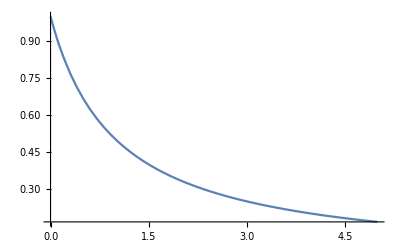

```mathematica
f[x_]:=1/(x+1)
Plot[f[x],{x,0,5}]
```

```mathematica
{Sum[f[k],{k,1,5}],Integrate[f[s],{s,0,5}],Sum[f[k],{k,0,4}]}//N
```

{1.45,1.79176,2.28333}

```mathematica
g[n_]:=Module[{v},If[n==2,
v="A",
If[n==3,
v="B",
v="Neither"
];
];
v
]/;IntegerQ[n]
```

## (* ERROR: - Enumerator for p q r - Dev - BUG *)

```mathematica
enumpq[n_]:=Module[{k=0,lst={}},
For[i=1,i<=n,i++,
For[j=1,j<i,j++,
k++;
lst=Append[lst,Prime[i]*Prime[j]];
];
];
lst
];
```

```mathematica
Select[enumpq[15],#<=100&]
```

{6,10,15,14,21,35,22,33,55,77,26,39,65,91,34,51,85,38,57,95,46,69,58,87,62,93,74,82,86,94}

```mathematica
enumpqr[n_]:=Module[{k=0,lst={}},
For[i=3,i<=n,i++,
For[j=1,j<=Prime[i],j++,
If[Mod[enumpq[[j]],Prime[i]]==0,Break[]];
k++;
Print[{k,l11[[j]]Prime[i]}];
];
]
]
```

## Bakjes-Info-[TBD]

```mathematica
viaPrt[n_]:=Flatten[Map[IntegerPartitions[#]&,Range[n]],1]
viaNum[n_]:=Module[{ls},
lst={};
For[i=2,i<n,i++,
lst=Append[lst,FactorInteger[i][[All,2]]]
];
Sort[DeleteDuplicates[DeleteDuplicates[lst,Sort[#1]==Sort[#2]&]]]
]

viaNum2[n_]:=Module[{ls},
lst={{0}};
For[i=2,i<(n+1),i++,
lst=Append[lst,Reverse[Sort[FactorInteger[i][[All,2]]]]]
];
lst
]

viaNum3[n_]:=Module[{ls},
lst={{0 ,{0}}};
For[i=2,i<(n+1),i++,
	lst=Append[lst,{Reverse[Sort[FactorInteger[i][[All,2]]]]}
]
];
lst
]
```

## Experiments: container (“Bakjes”) size

### Code to Transfer to Number Theory Package

```mathematica
nGetPrimeSignature[n_]:=Sort[FactorInteger[n][[All,2]]]

nBuildPrimeSignatureContainers[n_]:=Module[{assoc},
assoc=<|{0}->{1}|>;
If[
MissingQ[Lookup[assoc,{nGetPrimeSignature[#]}][[1]]],
assoc=AssociateTo[assoc,nGetPrimeSignature[#]->{#}],
assoc=AssociateTo[assoc,nGetPrimeSignature[#]->Append[Key[nGetPrimeSignature[#]][assoc],#]] 
]&/@Range[2,n];
assoc
]
```

### Alpha Tests

```mathematica
ds=nBuildPrimeSignatureContainers[100]//Dataset;
Normal[Values[KeySelect[ds,#=={1,1,1}&]]][[1]]//FactorInteger
```

{{{2,1},{3,1},{5,1}},{{2,1},{3,1},{7,1}},{{2,1},{3,1},{11,1}},{{2,1},{5,1},{7,1}},{{2,1},{3,1},{13,1}}}

### Building Subtrees

```mathematica
Prime[Range[PrimePi[10]]]
Normal[Values[KeySelect[ds,#=={1,1}&]]]
```

{2,3,5,7}

{{6,10,14,15,21,22,26}}

```mathematica
ls=(KeySelect[ds,#=={1,1}&]//Values//Normal)[[1]]

ls2=Select[ls,Not[Divisible[#,2]]&];
Complement[ls,ls2]

ls3=Select[ls2,Not[Divisible[#,3]]&];
Complement[ls2,ls3]

ls5=Select[ls3,Not[Divisible[#,5]]&];
Complement[ls3,ls5]

ls7=Select[ls5,Not[Divisible[#,7]]&];
Complement[ls5,ls7]

Union[ls,ls2,ls3,ls5,ls7]
FactorInteger[Union[ls,ls2,ls3,ls5,ls7]]
```

{6,10,14,15,21,22,26}

{6,10,14,22,26}

{15,21}

{}

{}

{6,10,14,15,21,22,26}

{{{2,1},{3,1}},{{2,1},{5,1}},{{2,1},{7,1}},{{3,1},{5,1}},{{3,1},{7,1}},{{2,1},{11,1}},{{2,1},{13,1}}}

## Bakjes R&D Devs

## temp-Specification

```mathematica
nGetPrimeSignature[n_]:=Sort[FactorInteger[n][[All,2]]]

nBuildPrimeSignatureContainers[n_]:=Module[
{assoc,k,prsig,m, tas, tas2, tasval},

assoc=<|{0}->{1}|>;
k=2;
prsig=nGetPrimeSignature[k];
If[
MissingQ[Lookup[assoc,{prsig}][[1]]],
AssociateTo[assoc,prsig->{k}],
assoc=AssociateTo[assoc,prsig->Append[Key[prsig][assoc],k]] ;
];

k=3;
prsig=nGetPrimeSignature[k];
If[
MissingQ[Lookup[assoc,{prsig}][[1]]],
AssociateTo[assoc,prsig->{k}],
assoc=AssociateTo[assoc,prsig->Append[Key[prsig][assoc],k]] ;
];

k=4;
prsig=nGetPrimeSignature[k];
If[
MissingQ[Lookup[assoc,{prsig}][[1]]],
AssociateTo[assoc,prsig->{k}],
assoc=AssociateTo[assoc,prsig->Append[Key[prsig][assoc],k]] ;
];

k=5;
prsig=nGetPrimeSignature[k];
If[
MissingQ[Lookup[assoc,{prsig}][[1]]],
AssociateTo[assoc,prsig->{k}],
assoc=AssociateTo[assoc,prsig->Append[Key[prsig][assoc],k]] ;
];

k=6;
prsig=nGetPrimeSignature[k];
m=Sort[FactorInteger[k][[All,1]]][[1]];
tas={Association[{m,"p"}->{k}]};
assoc=AssociateTo[assoc,prsig->tas];

k=7;
     prsig=nGetPrimeSignature[k];
     If[MissingQ[
Lookup[assoc,{prsig}][[1]]],
   AssociateTo[assoc,prsig->{k}],assoc=AssociateTo[assoc,prsig->Append[Key[prsig][assoc],k]];
];

k=8;
     prsig=nGetPrimeSignature[k];
     If[MissingQ[Lookup[assoc,{prsig}][[1]]],
AssociateTo[assoc,prsig->{k}],
assoc=AssociateTo[assoc,prsig->Append[Key[prsig][assoc],k]];
];

k=9;
     prsig=nGetPrimeSignature[k];
     If[MissingQ[Lookup[assoc,{prsig}][[1]]],
AssociateTo[assoc,prsig->{k}],
assoc=AssociateTo[assoc,prsig->Append[Key[prsig][assoc],k]];
];

assoc
]
out=nBuildPrimeSignatureContainers[2]
```

<|{0}→{1},{1}→{2,3,5,7},{2}→{4,9},{1,1}→{<|{2,p}→{6}|>},{3}→{8}|>

```mathematica
out
tas=out[{1,1}][[1]]
tas[{2,"p"}]=Append[tas[{2,"p"}],10]
```

<|{0}→{1},{1}→{2,3,5,7},{2}→{4,9},{1,1}→{<|{2,p}→{6}|>},{3}→{8}|>

<|{2,p}→{6}|>

{6,10}

## temp-Prototype

```mathematica
nGetPrimeSignature2[n_]:=Sort[FactorInteger[n][[All,2]]]

nBuildPrimeSignatureContainers[n_]:=Module[{assoc,k,prsig,m,p},

assoc=<|{0}->{1}|>;
For[k=2,k<=n,k++,
prsig=nGetPrimeSignature[k];
If[
MissingQ[Lookup[assoc,{prsig}][[1]]],
AssociateTo[assoc,prsig->{k}],
assoc=AssociateTo[assoc,prsig->Append[Key[prsig][assoc],k]] ;
];
];
assoc
]

                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                nBuildPrimeSignatureContainers[16]
```

<|{0}→{1},{1}→{2,3,5,7,11,13},{2}→{4,9},{1,1}→{6,10,14,15},{3}→{8},{1,2}→{12},{4}→{16}|>

## temp-DetailedTest

```mathematica
assoc=<|{0}->{1},{1}->{2,3,5},{2}->{4}|>
```

<|{0}→{1},{1}→{2,3,5},{2}→{4}|>

```mathematica
AssociationQ[assoc]
tst1={<|{2,"p"}->{6,10,14}|>};
tst2=Association[{3,"p"}->15];
tst1=Append[tst1,tst2]
```

True

{<|{2,p}→{6,10,14}|>,<|{3,p}→15|>}

## temp-Prototype2

```mathematica
Clear[prsig]
Clear[nPrimeSignatureToListOfIntegers]
```

```mathematica
nInitialize[init_]:=init
nPrimeSignatureToListOfIntegers[prsig_,k_]:=prsig->{k}
nAddPrsigIntlistToAssoc[lst_,assoc_]:=Association[assoc->lst]
```

## temp-Prototype3

```mathematica
init:=<| {0} -> {1} |>
nPtL[ps_,n_]:=ps->{n}
nAPL[as_,ls_]:=Association[as,ls]

assoc=nAPL[init,nPtL[{1},2]];
assoc[{1}]=Append[assoc[{1}],3];
assoc=nAPL[assoc,nPtL[{2},4]];
assoc[{1}]=Append[assoc[{1}],5];
tas=<|{2,"p"}->{6}|>;
assoc=nAPL[assoc,nPtL[{1,1},tas]];
assoc[{1}]=Append[assoc[{1}],7];
assoc=nAPL[assoc,nPtL[{3},8]];
assoc[{2}]=Append[assoc[{2}],9];
AppendTo[assoc[[Key@{1,1},1,Key@{2,"p"}]],10];
assoc[{1}]=Append[assoc[{1}],11];
assoc=nAPL[assoc,nPtL[{1,2},12]];
assoc[{1}]=Append[assoc[{1}],13];
AppendTo[assoc[[Key@{1,1},1,Key@{2,"p"}]],14];
tas=<|{3,"p"}->{15}|>;
assoc[{1,1}]=Append[assoc[{1,1}],tas];
assoc=nAPL[assoc,nPtL[{4},16]];
assoc[{1}]=Append[assoc[{1}],17];
assoc[{1,2}]=Append[assoc[{1,2}],18];
assoc[{1}]=Append[assoc[{1}],19];
assoc[{1,2}]=Append[assoc[{1,2}],20];
AppendTo[assoc[[Key@{1,1},2,Key@{3,"p"}]],21];
AppendTo[assoc[[Key@{1,1},1,Key@{2,"p"}]],22];
assoc[{1}]=Append[assoc[{1}],23];
assoc=nAPL[assoc,nPtL[{1,3},24]];
assoc[{2}]=Append[assoc[{2}],25];
AppendTo[assoc[[Key@{1,1},1,Key@{2,"p"}]],26];
assoc[{3}]=Append[assoc[{3}],27];
assoc[{1,2}]=Append[assoc[{1,2}],28];
assoc[{1}]=Append[assoc[{1}],29];
assoc=nAPL[assoc,nPtL[{1,1,1},30]];

assoc
```

<|{0}→{1},{1}→{2,3,5,7,11,13,17,19,23,29},{2}→{4,9,25},{1,1}→{<|{2,p}→{6,10,14,22,26}|>,<|{3,p}→{15,21}|>},{3}→{8,27},{1,2}→{12,18,20,28},{4}→{16},{1,3}→{24},{1,1,1}→{30}|>